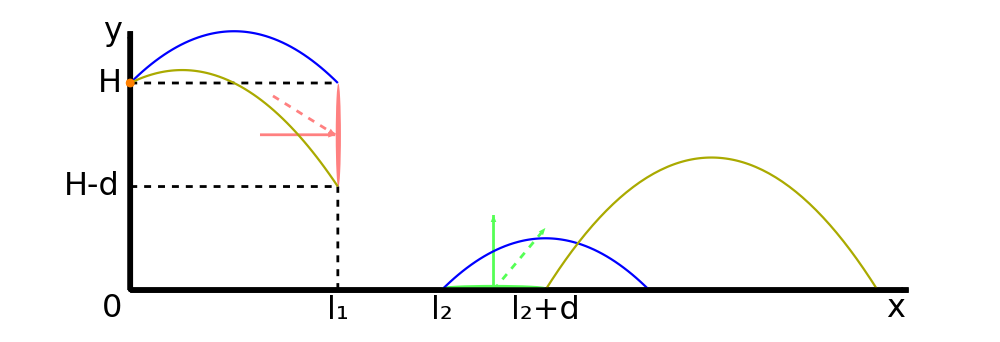

```mathematica
Show[Graphics[{Thickness[0.004],Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{3,0}}],Disk[{0,0},0.008],Orange,Disk[{0,0.8},0.017],Pink,Disk[{0.8,0.6},{0.01,0.2}],Lighter[Green],Disk[{1.4,0.01},{0.2,0.01}],Black,Thickness[0.002],Dashed,Line[{{0.8,0},{0.8,0.4}}],Line[{{0,0.4},{0.8,0.4}}],Line[{{0,0.8},{0.8,0.8}}],Text[Style["x",32,FontFamily->"TimesNewRoman",Italic],{2.95,-0.07}],Text[Style["y",32,FontFamily->"TimesNewRoman",Italic],{-0.07,1}],Text[Style["H",32,Italic,FontFamily->"TimesNewRoman"],{-0.08,0.8}],Text[Style["H-d",32,Italic,FontFamily->"TimesNewRoman"],{-0.15,0.4}],Text[Style["l_1",32,Italic,FontFamily->"TimesNewRoman"],{0.8,-0.08}],Text[Style["l_2",32,Italic,FontFamily->"TimesNewRoman"],{1.2,-0.08}],Text[Style["0",32,FontFamily->"TimesNewRoman"],{-0.07,-0.07}],Text[Style["l_2+d",32,FontFamily->"TimesNewRoman"],{1.6,-0.08}]},ImageSize->1000],Graphics[{Thickness[0.002],Pink,Arrowheads[0.02],Arrow[{{0.5,0.6},{0.79,0.6}}],Lighter[Green],Arrow[{{1.4,0},{1.4,0.29}}],Dashed,Pink,Arrow[{{0.55,0.75},{0.79,0.6}}],Lighter[Green],Arrow[{{1.4,0},{1.6,0.24}}]}],Plot[{0.8+x-5/4 x^2,0.8+0.5x-5/4 x^2},{x,0,0.8},PlotStyle->{Blue,Darker[Yellow]}],Plot[{(x-1.2)-5/4(x-1.2)^2},{x,1.2,2},PlotStyle->Blue],Plot[1.6(x-1.6)-5/4(x-1.6)^2,{x,1.6,2.88},PlotStyle->Darker[Yellow]],Graphics[{Thickness[0.004],Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{3,0}}],Disk[{0,0},0.008],Orange,Disk[{0,0.8},0.017]},ImageSize->1000]]
```

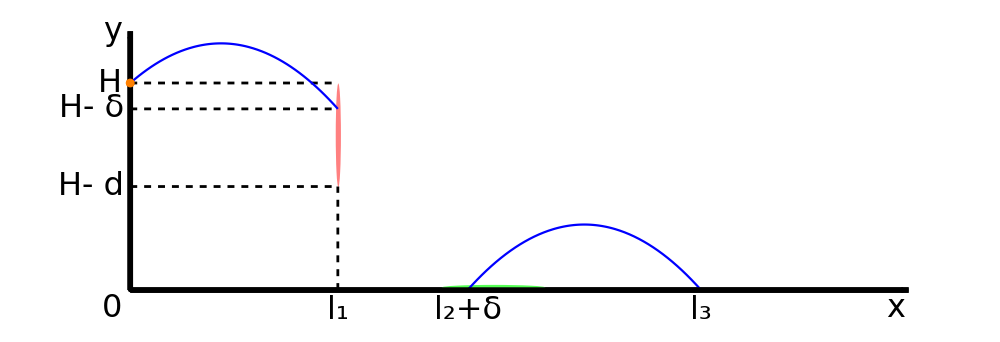

```mathematica
Show[Graphics[{Thickness[0.004],Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{3,0}}],Disk[{0,0},0.008],Orange,Disk[{0,0.8},0.017],Pink,Disk[{0.8,0.6},{0.01,0.2}],Lighter[Green],Disk[{1.4,0.01},{0.2,0.01}],Black,Thickness[0.002],Dashed,Line[{{0.8,0},{0.8,0.4}}],Line[{{0,0.4},{0.8,0.4}}],Line[{{0,0.8},{0.8,0.8}}],Line[{{0,0.7},{0.8,0.7}}],Text[Style["x",32,FontFamily->"TimesNewRoman",Italic],{2.95,-0.07}],Text[Style["y",32,FontFamily->"TimesNewRoman",Italic],{-0.07,1}],Text[Style["H",32,Italic,FontFamily->"TimesNewRoman"],{-0.08,0.8}],Text[Style["H- d",32,Italic,FontFamily->"TimesNewRoman"],{-0.15,0.4}],Text[Style["H- δ",32,Italic,FontFamily->"TimesNewRoman"],{-0.15,0.7}],Text[Style["l_1",32,Italic,FontFamily->"TimesNewRoman"],{0.8,-0.08}],Text[Style["0",32,FontFamily->"TimesNewRoman"],{-0.07,-0.07}],Text[Style["l_2+δ",32,FontFamily->"TimesNewRoman"],{1.3,-0.08}],Text[Style["l_3",32,FontFamily->"TimesNewRoman"],{2.2,-0.08}]},ImageSize->1000],Plot[{0.8+0.875x-5/4 x^2},{x,0,0.8},PlotStyle->Blue],Plot[{1.125(x-1.3)-5/4(x-1.3)^2},{x,1.3,2.2},PlotStyle->Blue],Graphics[{Thickness[0.004],Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{3,0}}],Disk[{0,0},0.008],Orange,Disk[{0,0.8},0.017]},ImageSize->1000]]
```

```mathematica
0.875-5/4 2x/.x->0.8
```

-1.125

```mathematica
Solve[4/5+a x-5/4 x^2==0.7/.x->0.8,a]
```

{{a→0.875}}

```mathematica
4/5+a x-5/4 x^2==0/.x->0.8
```

-1.11022×10^-16+0.8 a==0

```mathematica
1.125(x-1.3)-5/4(x-1.3)^2/.x->2.2
```

-2.22045×10^-16